## Definitions

```mathematica
op[x_,loc_]:=Text[Style[x,13,Bold,Italic,Background->White,FontFamily->"Arial"],loc]
```

```mathematica
op[x_,loc_,weight_]:=Text[Style[x,13,weight,Italic,Background->White,FontFamily->"Arial"],loc]
```

```mathematica
op[x_,loc_,weight_,color_]:=Text[Style[x,13,weight,color,Italic,Background->White,FontFamily->"Arial"],loc]
```

```mathematica
op["x",{0,1}]
```

Text[x,{0,1}]

```mathematica
fsize=14
```

14

```mathematica
size:=120;
```

```mathematica
sb=.1( 120/size); ah=.04;
```

```mathematica
{size,ah,sb}//N
```

{120.,0.04,0.1}

```mathematica
Text[Style[α, 16], .5(la+lb),Background->White]
```

```mathematica
lab[n_,p1_,p2_]:=Text[Style[StringJoin[" ",ToString[n]," "],fsize,FontFamily->"Arial"],.5(p1+p2),Background->White]
```

## Construction of commutative squares

```mathematica
la={0,1};ra={1,1};
lb={0,0};rb={1,0};
rra={2,1};rrb={2,0};
```

```mathematica
funcdi[list_,size_]:=Framed[Graphics[
{Arrowheads[Medium],list},
ImageSize->size,FrameTicks->False],FrameMargins->Tiny, FrameStyle->White]
```

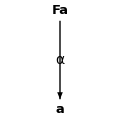

```mathematica
alg=funcdi[{
op["Fa",la],op["a",lb],Arrow[{la,lb},sb],lab[α,la,lb]},{size,size}]
```

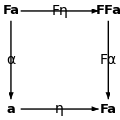

```mathematica
firstdi=funcdi[{
op["Fa",la],op["FFa",ra],op["a",lb],op["Fa",rb],
Arrow[{la,ra},sb],Arrow[{lb,rb},sb],Arrow[{la,lb},sb],Arrow[{ra,rb},sb],lab[α,la,lb],lab[Fη,la,ra],lab[η,lb,rb],lab[Fα,ra,rb]},{size,size}]
```

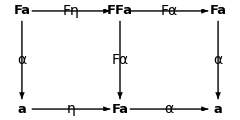

```mathematica
seconddi=funcdi[{
op["Fa",la],op["FFa",ra],op["a",lb],op["Fa",rb],op["Fa",rra],op["a",rrb],
Arrow[{la,ra},sb],Arrow[{lb,rb},sb],Arrow[{la,lb},sb],Arrow[{ra,rb},sb],Arrow[{ra,rra},sb],Arrow[{rra,rrb},sb],Arrow[{rb,rrb},sb],lab[α,la,lb],lab[Fη,la,ra],lab[η,lb,rb],lab[Fα,ra,rb],lab[Fα,ra,rra],lab[α,rra,rrb],lab[α,rb,rrb]},{2 size,size}]
```

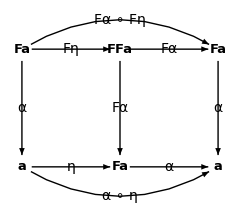

```mathematica
thirddi=funcdi[{
op["Fa",la],op["FFa",ra],op["a",lb],op["Fa",rb],op["Fa",rra],op["a",rrb],
Arrow[{la,ra},sb],Arrow[{lb,rb},sb],Arrow[{la,lb},sb],Arrow[{ra,rb},sb],Arrow[{ra,rra},sb],Arrow[{rra,rrb},sb],Arrow[{rb,rrb},sb],
Arrow[BezierCurve[{la,{1,1.5},rra}],sb],
Arrow[BezierCurve[{lb,{1,-.5},rrb}],sb],
lab[α,la,lb],lab[Fη,la,ra],lab[η,lb,rb],lab[Fα,ra,rb],lab[Fα,ra,rra],lab[α,rra,rrb],lab[α,rb,rrb],lab[Fα∘Fη,ra,{1,1.5}],lab[α∘η,rb,{1,-.5}]},{2size,1.8size}]
```

α∘η  must be id_a by the fact that α is initial, so η is a right inverse to α. The left square says that  η∘α must be F(α)∘F(η) which is F(α∘η)=F(id_a)=id_F(a), so η must be also a left inverse to α.  So α is an isomorphism.

```mathematica
id_Fa
```

id_Fa

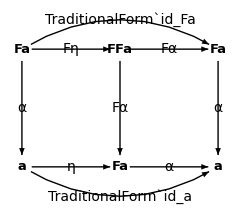

```mathematica
fourthdi=funcdi[{
op["Fa",la],op["FFa",ra],op["a",lb],op["Fa",rb],op["Fa",rra],op["a",rrb],
Arrow[{la,ra},sb],Arrow[{lb,rb},sb],Arrow[{la,lb},sb],Arrow[{ra,rb},sb],Arrow[{ra,rra},sb],Arrow[{rra,rrb},sb],Arrow[{rb,rrb},sb],
Arrow[BezierCurve[{la,{1,1.5},rra}],sb],
Arrow[BezierCurve[{lb,{1,-.5},rrb}],sb],
lab[α,la,lb],lab[Fη,la,ra],lab[η,lb,rb],lab[Fα,ra,rb],lab[Fα,ra,rra],lab[α,rra,rrb],lab[α,rb,rrb],lab[Subscript[id, Fa]//TraditionalForm,ra,{1,1.5}],lab[Subscript[id, a]//TraditionalForm,rb,{1,-.5}]
},{2size,1.8size}]
```

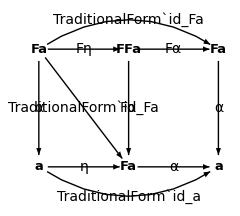

```mathematica
fifthdi=funcdi[{
op["Fa",la],op["FFa",ra],op["a",lb],op["Fa",rb],op["Fa",rra],op["a",rrb],
Arrow[{la,ra},sb],Arrow[{lb,rb},sb],Arrow[{la,lb},sb],Arrow[{ra,rb},sb],Arrow[{ra,rra},sb],Arrow[{rra,rrb},sb],Arrow[{rb,rrb},sb],
Arrow[BezierCurve[{la,{1,1.5},rra}],sb],
Arrow[BezierCurve[{lb,{1,-.5},rrb}],sb],
Arrow[{la,rb},sb],
lab[α,la,lb],lab[Fη,la,ra],lab[η,lb,rb],lab[Fα,ra,rb],lab[Fα,ra,rra],lab[α,rra,rrb],lab[α,rb,rrb],lab[Subscript[id, Fa]//TraditionalForm,ra,{1,1.5}],lab[Subscript[id, a]//TraditionalForm,rb,{1,-.5}],lab[Subscript[id, Fa]//TraditionalForm,la,rb]
},{2size,1.8size}]
```

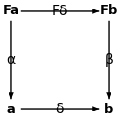

```mathematica
sixthdi=funcdi[{
op["Fa",la],op["Fb",ra],op["a",lb],op["b",rb],
Arrow[{la,ra},sb],Arrow[{lb,rb},sb],Arrow[{la,lb},sb],Arrow[{ra,rb},sb],lab[α,la,lb],lab[Fδ,la,ra],lab[δ,lb,rb],lab[β,ra,rb]},{size,size}]
```

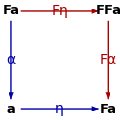

```mathematica
seventhdi=firstdi=funcdi[{
op["Fa",la],op["FFa",ra],op["a",lb],op["Fa",rb],Red//Darker,
Arrow[{la,ra},sb],Arrow[{ra,rb},sb],Blue//Darker,,Arrow[{la,lb},sb],Arrow[{lb,rb},sb],lab[α,la,lb],lab[η,lb,rb],Red//Darker,lab[Fα,ra,rb],lab[Fη,la,ra]},{size,size}]
```

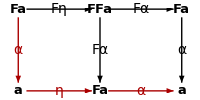

```mathematica
eighthdi=funcdi[{
op["Fa",la],op["FFa",ra],op["a",lb],op["Fa",rb],op["Fa",rra],op["a",rrb],
Thick,Red//Darker,Arrow[{la,lb},sb],Arrow[{rb,rrb},sb],Arrow[{lb,rb},sb],Thin,Black,Arrow[{la,ra},sb],Arrow[{ra,rb},sb],Arrow[{ra,rra},sb],Arrow[{rra,rrb},sb],Thick,Red//Darker,lab[α,rb,rrb],lab[α,la,lb],lab[η,lb,rb],Thin,Black,lab[α,rra,rrb],lab[Fη,la,ra],lab[Fα,ra,rb],lab[Fα,ra,rra]},{200,100}]
```

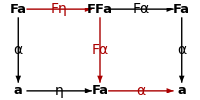

```mathematica
ninthdi=funcdi[{
op["Fa",la],op["FFa",ra],op["a",lb],op["Fa",rb],op["Fa",rra],op["a",rrb],Thick,
Red//Darker,Arrow[{la,ra},sb],Arrow[{ra,rb},sb],Arrow[{rb,rrb},sb],Thin,Black,Arrow[{rra,rrb},sb],Arrow[{ra,rra},sb],Arrow[{lb,rb},sb],Arrow[{la,lb},sb],lab[α,la,lb],Thick,Red//Darker,lab[Fα,ra,rb],lab[α,rb,rrb],lab[Fη,la,ra],Thin,Black,lab[Fα,ra,rra],lab[α,rra,rrb],lab[η,lb,rb]},{200,100}]
```

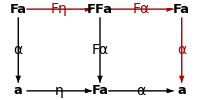

```mathematica
tenthdi=funcdi[{
op["Fa",la],op["FFa",ra],op["a",lb],op["Fa",rb],op["Fa",rra],op["a",rrb],
Thick,Red//Darker,Arrow[{la,ra},sb],Arrow[{ra,rra},sb],Arrow[{rra,rrb},sb],Thin,Black,Arrow[{lb,rb},sb],Arrow[{la,lb},sb],Arrow[{ra,rb},sb],Arrow[{rb,rrb},sb],lab[α,la,lb],Thick,Red//Darker,lab[Fη,la,ra],lab[Fα,ra,rra],lab[α,rra,rrb],Thin,Black,lab[η,lb,rb],lab[Fα,ra,rb],lab[α,rb,rrb]},{200,100}]
```

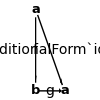

```mathematica
elevdi=funcdi[{op["a",la],op["b",lb],op["a",rb],
Arrow[{la,rb},sb],Arrow[{la,lb},sb],Arrow[{lb,rb},sb],lab[f,la,lb],lab[g,lb,rb],lab[Subscript[id, a]//TraditionalForm,la,rb]},{100,100}]
```

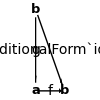

```mathematica
twelvdi=funcdi[{op["b",la],op["a",lb],op["b",rb],
Arrow[{la,rb},sb],Arrow[{la,lb},sb],Arrow[{lb,rb},sb],lab[g,la,lb],lab[f,lb,rb],lab[Subscript[id, b]//TraditionalForm,la,rb]},{100,100}]
```